```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*Define Constants*)
kB:=8.6173324*10^-5 (*[ev/K]*)
hbar:=6.58211928*10^-16 (*[eV*s]*)
vc:=299792458 (*[m/s]*)
T0:=273.15 (*[K]*)
```

## Plot Spectra

```mathematica
SiData=ReadList["Si_richtig_1.ssm",{Real,Real}];
CaF2Data=ReadList["CaF2_1.SSM",{Real,Real}];
GraphitData=ReadList["Graphit_1.ssm",{Real,Real}];
```

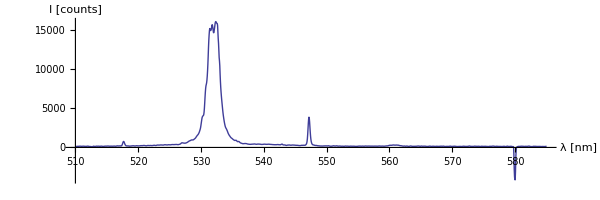

```mathematica
ListLinePlot[SiData,PlotRange->All,AspectRatio->1/3,AxesLabel->{"λ [nm]","I [counts]"}]
```

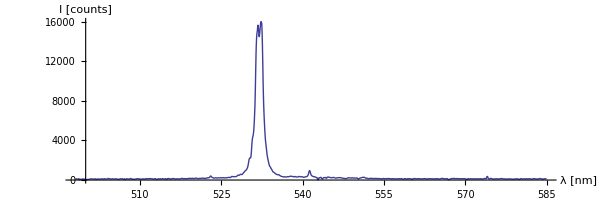

```mathematica
ListLinePlot[CaF2Data,PlotRange->All,AspectRatio->1/3,AxesLabel->{"λ [nm]","I [counts]"}]
```

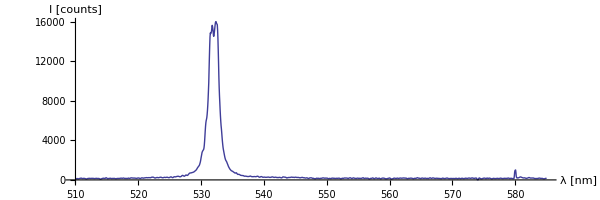

```mathematica
ListLinePlot[GraphitData,PlotRange->All,ImageSize->600,AspectRatio->1/3,AxesLabel->{"λ [nm]","I [counts]"}]
```

## Fit Peaks with Lorentzian

### Silicium

#### Rayleigh Peak

121.037+116771./(1+11.111 (-531.986+x)^2)

110055.

| Estimate | Standard Error | t-Statistic | P-Value
x0 | 531.986 | 0.00316962 | 167839. | 2.95892220345×10^-1564
a | 116771. | 24876.5 | 4.69404 | 3.69111×10^-6
b | 0.300001 | 0.0339441 | 8.83808 | 3.1734×10^-17
c | 121.037 | 11.2849 | 10.7255 | 9.54754×10^-24

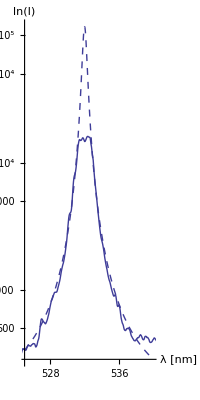

```mathematica
FittDataLaserSi=ReadList["Laserpeak_Si.txt",{Real,Real}];
PlotDataLaserSi=ReadList["Plot_Laserpeak_Si.txt",{Real,Real}];
Normal[LaserPeakSi=NonlinearModelFit[FittDataLaserSi,a/(1+((x-x0)/b)^2)+c,{{x0,532},{a,5*16000},{b,2},c},x]]
ItotLaserPeakSi=Re[Integrate[LaserPeakSi[x]-LaserPeakSi["ParameterTable"][[1,1,5,2]],{x,-Infinity,Infinity}]]
LaserPeakSi["ParameterTable"]
Show[LogPlot[Normal[LaserPeakSi],{x,525,540},PlotStyle->Dashed,PlotRange->All,AspectRatio->2],ListLogPlot[PlotDataLaserSi,PlotRange->All,Joined->True],AxesLabel->{"λ [nm]","ln(I)"},ImageSize->200]
```

#### Stokes Peak

-48.9613+4051.3/(1+29.8954 (-547.202+x)^2)

| Estimate | Standard Error | t-Statistic | P-Value
x0 | 547.202 | 0.00304588 | 179653. | 4.32408×10^-124
a | 4051.3 | 71.8146 | 56.4133 | 1.48087×10^-29
b | 0.182893 | 0.00666062 | 27.4589 | 2.89756×10^-21
c | -48.9613 | 45.7216 | -1.07086 | 0.293713

2327.78

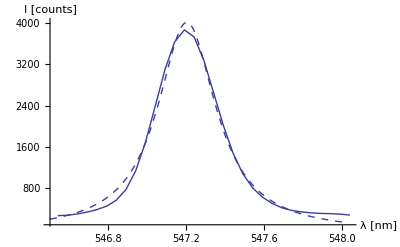

```mathematica
FittDataStokesSi=ReadList["Stokespeak_Si.txt",{Real,Real}];
ListLinePlot[FittDataStokesSi,PlotRange->All];
Normal[StokesPeakSi=NonlinearModelFit[FittDataStokesSi,a/(1+((x-x0)/b)^2)+c,{{x0,547},{a,3800},{b,.5},{c,270}},x]]
StokesPeakSi["ParameterTable"]
ItotStokesPeakSi=Re[Integrate[StokesPeakSi[x]-StokesPeakSi["ParameterTable"][[1,1,5,2]],{x,-Infinity,Infinity}]]
Show[Plot[Normal[StokesPeakSi],{x,546.5,548},PlotStyle->Dashed,PlotRange->All],ListLinePlot[FittDataStokesSi,PlotRange->All],AxesLabel->{"λ [nm]","I [counts]"},ImageSize->400]
```

#### 2 nd Order Stokes Peak

89.6437+223.491/(1+0.666393 (-560.811+x)^2)

| Estimate | Standard Error | t-Statistic | P-Value
x0 | 560.811 | 0.0155016 | 36177.7 | 3.86601×10^-280
a | 223.491 | 9.2523 | 24.1552 | 1.11918×10^-37
b | 1.225 | 0.0762882 | 16.0575 | 2.72842×10^-26
c | 89.6437 | 10.206 | 8.7834 | 3.13716×10^-13

860.093

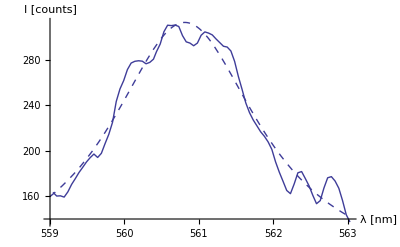

```mathematica
FittDataStokes2ndOrderSi=ReadList["2nd_Stokespeak_Si.txt",{Real,Real}];
ListLinePlot[FittDataStokes2ndOrderSi,PlotRange->All];
Normal[Stokes2ndOrderPeakSi=NonlinearModelFit[FittDataStokes2ndOrderSi,a/(1+((x-x0)/b)^2)+c,{{x0,560},{a,300},{b,3},c},x]]
Stokes2ndOrderPeakSi["ParameterTable"]
ItotStokes2nOrderPeakPeakSi=Re[Integrate[Stokes2ndOrderPeakSi[x]-Stokes2ndOrderPeakSi["ParameterTable"][[1,1,5,2]],{x,-Infinity,Infinity}]]
Show[Plot[Normal[Stokes2ndOrderPeakSi],{x,559,563},PlotStyle->Dashed,PlotRange->All],ListLinePlot[FittDataStokes2ndOrderSi,PlotRange->All],AxesLabel->{"λ [nm]","I [counts]"},ImageSize->400]
```

#### Anti-Stokes Peak

137.019+662.984/(1+37.2553 (-517.679+x)^2)

| Estimate | Standard Error | t-Statistic | P-Value
x0 | 517.679 | 0.00368987 | 140297. | 3.43012×10^-121
a | 662.984 | 15.5606 | 42.6065 | 2.66824×10^-26
b | 0.163835 | 0.00768781 | 21.311 | 2.02499×10^-18
c | 137.019 | 8.81746 | 15.5395 | 5.45473×10^-15

341.239

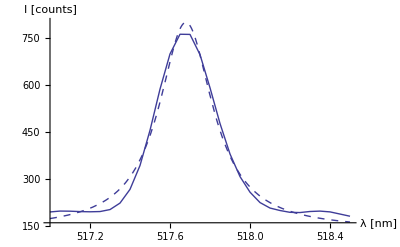

```mathematica
FittDataAntistokesSi=ReadList["Antistokespeak_Si.txt",{Real,Real}];
ListLinePlot[FittDataAntistokesSi,PlotRange->All];
Normal[AntistokesPeakSi=NonlinearModelFit[FittDataAntistokesSi,a/(1+((x-x0)/b)^2)+c,{{x0,517},{a,700},{b},c},x]]
AntistokesPeakSi["ParameterTable"]
ItotAntistokesPeakSi=Re[Integrate[AntistokesPeakSi[x]-AntistokesPeakSi["ParameterTable"][[1,1,5,2]],{x,-Infinity,Infinity}]]
Show[Plot[Normal[AntistokesPeakSi],{x,517,518.5},PlotStyle->Dashed,PlotRange->All],ListLinePlot[FittDataAntistokesSi,PlotRange->All],AxesLabel->{"λ [nm]","I [counts]"},ImageSize->400]
```

#### Calculating Intensity Ratios

```mathematica
ItotStokesPeakSi/(10^5*ItotLaserPeakSi)
ItotStokesPeakSi/(10^6*ItotLaserPeakSi)
```

2.11511×10^-7

2.11511×10^-8

```mathematica
ItotAntistokesPeakSi/ItotStokesPeakSi
```

0.146594

```mathematica
(kB/(64.2*10^-3)*Log[ItotStokesPeakSi/ItotAntistokesPeakSi])^-1
```

388.008

```mathematica
%-T0
```

114.858

### CaF_2

#### Rayleigh Peak

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

165.895+(1.03456×10^6)/(1+195.027 (-531.986+x)^2)

| Estimate | Standard Error | t-Statistic | P-Value
x0 | 531.986 | 0.00471747 | 112769. | 2.256349190592×10^-1481
a | 1.03456×10^6 | 6.24368×10^6 | 0.165698 | 0.86848
b | -0.0716066 | 0.216846 | -0.330219 | 0.74141
c | 165.895 | 9.47997 | 17.4995 | 3.81972×10^-51

232734.

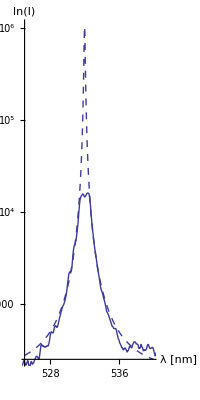

```mathematica
FittDataLaserCaF2=ReadList["Laserpeak_CaF2.txt",{Real,Real}];
PlotDataLaserCaF2=ReadList["Plot_Laserpeak_CaF2.txt",{Real,Real}];
Normal[LaserPeakCaF2=NonlinearModelFit[FittDataLaserCaF2,a/(1+((x-x0)/b)^2)+c,{{x0,532},{a,5*16000},{b,2},c},x]]
LaserPeakCaF2["ParameterTable"]
ItotLaserPeakCaF2=Re[Integrate[LaserPeakCaF2[x]-LaserPeakCaF2["ParameterTable"][[1,1,5,2]],{x,-Infinity,Infinity}]]
Show[LogPlot[Normal[LaserPeakCaF2],{x,525,540},PlotStyle->Dashed,PlotRange->All,AspectRatio->2],ListLogPlot[PlotDataLaserCaF2,PlotRange->All,Joined->True],ImageSize->200,AxesLabel->{"λ [nm]","ln(I)"}]
```

#### Stokes Peak

273.446+696.42/(1+22.2033 (-541.303+x)^2)

| Estimate | Standard Error | t-Statistic | P-Value
x0 | 541.303 | 0.00279469 | 193690. | 3.18895×10^-168
a | 696.42 | 9.52272 | 73.1325 | 1.26062×10^-41
b | 0.212222 | 0.0056678 | 37.4435 | 5.10255×10^-31
c | 273.446 | 5.1254 | 53.3513 | 1.3218×10^-36

464.314

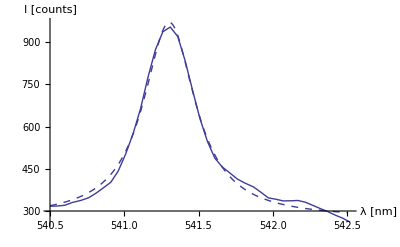

```mathematica
FittDataStokesCaF2=ReadList["Stokespeak_CaF2.txt",{Real,Real}];
ListLinePlot[FittDataStokesCaF2,PlotRange->All];
Normal[StokesPeakCaF2=NonlinearModelFit[FittDataStokesCaF2,a/(1+((x-x0)/b)^2)+c,{{x0,541},{a,900},{b,.7},{c}},x]]
StokesPeakCaF2["ParameterTable"]
ItotStokesPeakCaF2=Re[Integrate[StokesPeakCaF2[x]-StokesPeakCaF2["ParameterTable"][[1,1,5,2]],{x,-Infinity,Infinity}]]
Show[Plot[Normal[StokesPeakCaF2],{x,540.5,542.5},PlotStyle->Dashed,PlotRange->All],ListLinePlot[FittDataStokesCaF2,PlotRange->All],ImageSize->400,AxesLabel->{"λ [nm]","I [counts]"}]
```

#### Anti - Stokes Peak

202.572+211.99/(1+38.7137 (-523.065+x)^2)

| Estimate | Standard Error | t-Statistic | P-Value
x0 | 523.065 | 0.003899 | 134154. | 3.71459×10^-78
a | 211.99 | 6.07576 | 34.8912 | 2.91399×10^-17
b | 0.160719 | 0.00995176 | 16.1498 | 9.53758×10^-12
c | 202.572 | 5.09896 | 39.7281 | 3.28866×10^-18

107.037

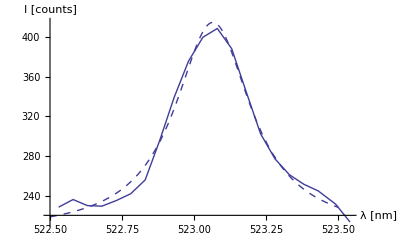

```mathematica
FittDataAntistokesCaF2=ReadList["Antistokespeak_CaF2.txt",{Real,Real}];
ListLinePlot[FittDataAntistokesCaF2,PlotRange->All];
Normal[AntistokesPeakCaF2=NonlinearModelFit[FittDataAntistokesCaF2,a/(1+((x-x0)/b)^2)+c,{{x0,523},{a,400},{b,0.7},c},x]]
AntistokesPeakCaF2["ParameterTable"]
ItotAntistokesPeakCaF2=Re[Integrate[AntistokesPeakCaF2[x]-AntistokesPeakCaF2["ParameterTable"][[1,1,5,2]],{x,-Infinity,Infinity}]]
Show[Plot[Normal[AntistokesPeakCaF2],{x,522.5,523.5},PlotStyle->Dashed,PlotRange->All],ListLinePlot[FittDataAntistokesCaF2,PlotRange->All],ImageSize->400,AxesLabel->{"λ [nm]","I [counts]"}]
```

#### Calculating Intensity Ratios

```mathematica
ItotStokesPeakCaF2/(10^5*ItotLaserPeakCaF2)
ItotStokesPeakCaF2/(10^6*ItotLaserPeakCaF2)
```

1.99504×10^-8

1.99504×10^-9

```mathematica
ItotStokesPeakCaF2/ItotAntistokesPeakCaF2
```

4.33789

```mathematica
((1000*kB)/39.85*Log[ItotStokesPeakCaF2/ItotAntistokesPeakCaF2])^-1
```

315.145

```mathematica
%-T0
```

41.9948

### Graphite

#### Rayleigh Peak

112.562+129047./(1+16.4957 (-531.986+x)^2)

| Estimate | Standard Error | t-Statistic | P-Value
x0 | 531.986 | 0.00272942 | 194908. | 5.289507227364×10^-1575
a | 129047. | 37436.5 | 3.44709 | 0.000627704
b | 0.246215 | 0.0371951 | 6.61956 | 1.18078×10^-10
c | 112.562 | 7.56372 | 14.8819 | 4.60106×10^-40

99818.9

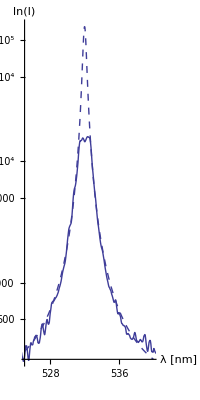

```mathematica
FittDataLaserGraphite=ReadList["Laserpeak_Graphite.txt",{Real,Real}];
PlotDataLaserGraphite=ReadList["Plot_Laserpeak_Graphite.txt",{Real,Real}];
Normal[LaserPeakGraphite=NonlinearModelFit[FittDataLaserGraphite,a/(1+((x-x0)/b)^2)+c,{{x0,532},{a,5*16000},{b,2},c},x]]
LaserPeakGraphite["ParameterTable"]
ItotLaserPeakGraphite=Re[Integrate[LaserPeakGraphite[x]-LaserPeakGraphite["ParameterTable"][[1,1,5,2]],{x,-Infinity,Infinity}]]
Show[LogPlot[Normal[LaserPeakGraphite],{x,525,540},PlotStyle->Dashed,PlotRange->All,AspectRatio->2],ListLogPlot[PlotDataLaserGraphite,PlotRange->All,Joined->True],AxesLabel->{"λ [nm]","ln(I)"},ImageSize->200]
```

#### Stokes Peak

60.1987+1040.84/(1+76.6969 (-580.032+x)^2)

| Estimate | Standard Error | t-Statistic | P-Value
x0 | 580.032 | 0.00702474 | 82569.8 | 1.42293×10^-74
a | 1040.84 | 67.0041 | 15.534 | 1.77507×10^-11
b | 0.114186 | 0.0148701 | 7.67886 | 6.34695×10^-7
c | 60.1987 | 39.4501 | 1.52594 | 0.145413

373.375

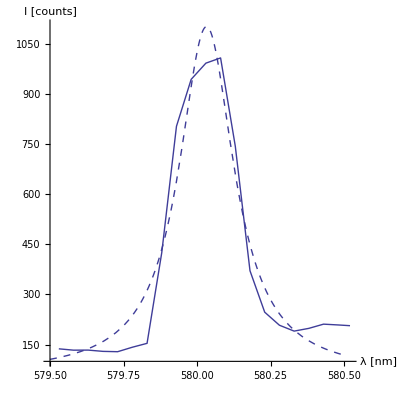

```mathematica
FittDataStokesGraphite=ReadList["Stokespeak_Graphite.txt",{Real,Real}];
ListLinePlot[FittDataStokesGraphite,PlotRange->All];
Normal[StokesPeakGraphite=NonlinearModelFit[FittDataStokesGraphite,a/(1+((x-x0)/b)^2)+c,{{x0,580},{a,1000},{b,.4},{c,100}},x]]
StokesPeakGraphite["ParameterTable"]
ItotStokesPeakGraphite=Re[Integrate[StokesPeakGraphite[x]-StokesPeakGraphite["ParameterTable"][[1,1,5,2]],{x,-Infinity,Infinity}]]
Show[Plot[Normal[StokesPeakGraphite],{x,579.5,580.5},PlotStyle->Dashed,PlotRange->All],ListLinePlot[FittDataStokesGraphite,PlotRange->All],ImageSize->400,AxesLabel->{"λ [nm]","I [counts]"},AspectRatio->1]
```

#### Calculating Intensity Ratios

```mathematica
ItotStokesPeakGraphite/(10^5 ItotLaserPeakGraphite)
ItotStokesPeakGraphite/(10^6 ItotLaserPeakGraphite)
```

3.74052×10^-8

3.74052×10^-9